# Amplitudes and Probability without Andreev approximation

```mathematica
H=h*v*Z;
v=1/m;
p=Solve[{1+b==c*u0+d*v0,a==c*v0+d*u0,c*q1*u0-d*q2*v0-k1+b*k1==-I*2*Z*(1+b),c*q1*v0-q2*d*u0-a*k2==-I*2*Z*a},{a,b,c,d}]//Simplify;
a=a/.p[[1]]//Simplify
b=b/.p[[1]]//Simplify
c=c/.p[[1]]//Simplify
d=d/.p[[1]]//Simplify
```

-(2 k1 (q1+q2) u0^2 v0)/((q1+q2) u0 v0^2 (-k1+q2-2 ⅈ Z)+u0 (-u0^2 (k1+q1+2 ⅈ Z)+v0^2 (k1-q2+2 ⅈ Z)) (k2+q2-2 ⅈ Z))

(-(u0^2-v0^2) (q2-2 ⅈ Z) (q1+2 ⅈ Z)+k1 (q2 u0^2+q1 v0^2+k2 (u0^2-v0^2)-2 ⅈ u0^2 Z+2 ⅈ v0^2 Z)-k2 (q1 u0^2+q2 v0^2+2 ⅈ (u0^2-v0^2) Z))/((u0^2-v0^2) (q2-2 ⅈ Z) (q1+2 ⅈ Z)+k1 (q2 u0^2+q1 v0^2+k2 (u0^2-v0^2)-2 ⅈ u0^2 Z+2 ⅈ v0^2 Z)+k2 (q1 u0^2+q2 v0^2+2 ⅈ (u0^2-v0^2) Z))

(2 k1 u0 (k2+q2-2 ⅈ Z))/((u0^2-v0^2) (q2-2 ⅈ Z) (q1+2 ⅈ Z)+k1 (q2 u0^2+q1 v0^2+k2 (u0^2-v0^2)-2 ⅈ u0^2 Z+2 ⅈ v0^2 Z)+k2 (q1 u0^2+q2 v0^2+2 ⅈ (u0^2-v0^2) Z))

-(2 k1 v0 (k2-q1-2 ⅈ Z))/((u0^2-v0^2) (q2-2 ⅈ Z) (q1+2 ⅈ Z)+k1 (q2 u0^2+q1 v0^2+k2 (u0^2-v0^2)-2 ⅈ u0^2 Z+2 ⅈ v0^2 Z)+k2 (q1 u0^2+q2 v0^2+2 ⅈ (u0^2-v0^2) Z))

# NIS to NIN in the limit u->1, v->0, Here, A becomes zero and B is non-zero. In this limit q_e=k_e.

```mathematica
A1=Abs[a]^2/.{u0->1,v0->0}
```

0

```mathematica
B1=ComplexExpand[b*Conjugate[b]]/.{u0->1,v0->0, k1->q1}//Simplify
```

Z^2/(q1^2+Z^2)

# Conservation of Probability

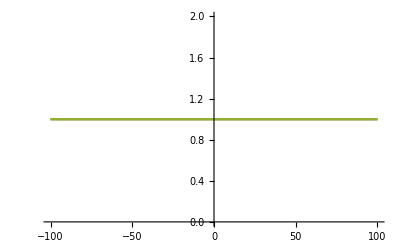

```mathematica
u0=Piecewise[{{(1/2*(1+I((-G^2+Δs^2)/G^2)^(1/2)))^(1/2),G^2< Δs^2},{(1/2*(1+((G^2-Δs^2)/G^2)^(1/2)))^(1/2),G^2> Δs^2 }}];

v0=Piecewise[{{(1/2*(1-I((-G^2+Δs^2)/G^2)^(1/2)))^(1/2),G^2< Δs^2},{(1/2*(1-((G^2-Δs^2)/G^2)^(1/2)))^(1/2),G^2> Δs^2 }}]; 


q11=Piecewise[{{(1-((G^2-Δs^2)^(1/2))/Ef)^(1/2),(G^2-Δs^2)<Ef},{(1+((G^2-Δs^2)^(1/2))/Ef)^(1/2),(G^2-Δs^2)≥  Ef }}];
q12=Piecewise[{{(1-(I*(Δs^2-G^2)^(1/2))/Ef)^(1/2),(Δs^2-G^2)<Ef},{(1+(I*(Δs^2-G^2)^(1/2))/Ef)^(1/2),(Δs^2-G^2)≥  Ef }}];

q1=Piecewise[{{q12,G^2<Δs^2},{q11,Δs^2≤ G^2}}];


q21=Piecewise[{{(1-((G^2-Δs^2)^(1/2))/Ef)^(1/2),(G^2-Δs^2)<Ef},{(1+((G^2-Δs^2)^(1/2))/Ef)^(1/2),(G^2-Δs^2)≥  Ef }}];
q22=Piecewise[{{(1-(I*(Δs^2-G^2)^(1/2))/Ef)^(1/2),(Δs^2-G^2)<Ef},{(1+(I*(Δs^2-G^2)^(1/2))/Ef)^(1/2),(Δs^2-G^2)≥  Ef }}];

q2=Piecewise[{{q22,G^2<Δs^2},{q21,Δs^2≤ G^2}}];


(* q1=Piecewise[{{(1+(I*(-G^2+Δs^2)^(1/2))/Ef)^(1/2),G^2< Δs^2},{(1+((G^2-Δs^2)^(1/2))/Ef)^(1/2),G^2> Δs^2 }}];

q2=Piecewise[{{(1-(I*(-G^2+Δs^2)^(1/2))/Ef)^(1/2),G^2< Δs^2},{(1-((G^2-Δs^2)^(1/2))/Ef)^(1/2),G^2> Δs^2 }}];  *)
k1=Piecewise[{{(1+G/Ef)^(1/2),G>Ef},{(1-G/Ef)^(1/2),G<=Ef}}];
k2=Piecewise[{{(1+G/Ef)^(1/2),G>Ef},{(1-G/Ef)^(1/2),G<=Ef}}];
k=8.617*10^-5;
Tc=9.2;
△=1.76*k*Tc;  
Ef=100*△;
Δs=△;
Reh=Abs[a]^2//Simplify;
Ree=Abs[b]^2//Simplify;
Tee=Abs[q1/k1](Abs[u0]^2-Abs[v0]^2)Abs[c]^2;
Teh=Abs[q2/k1](Abs[u0]^2-Abs[v0]^2)Abs[d]^2;
Pr=Ree+Reh+Tee+Teh;
Plot[{(Pr)/.{Z-> 0.01},(Pr)/.{Z-> 2.0},(Pr)/.{Z-> 5.0}},{G,-100,100},PlotRange->{0,2}]
```

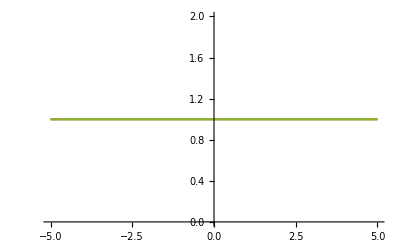

```mathematica
Plot[{(Pr)/.{G->100},(Pr)/.{G->1},(Pr)/.{G->0.01}},{Z,-5,5},PlotRange->{0,2}]
```

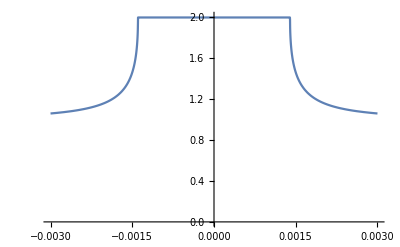

```mathematica
Plot[(1-Ree+Reh)/.{Z-> 0.0},{G,-0.003,0.003},PlotRange->{0,2.01}]
```

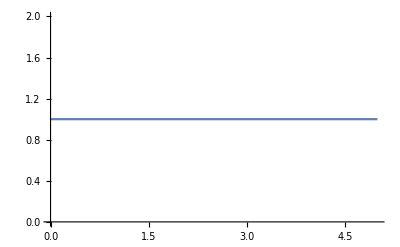

```mathematica
Plot[(Ree+Reh+Tee+Teh)/.{G->-100*Δs},{Z,0,5},PlotRange->{0,2}]
```

```mathematica
(Ree+Reh+Tee+Teh)/.{G->1,Z->0}
```

1.

## Δ_T noise in NIS & NIN junction at finite temperature

```mathematica
T1=4;
T2=3;
A=-(2 k1 (q1+q2) u0^2 v0)/((q1+q2) u0 v0^2 (-k1+q2-2 ⅈ Z)+u0 (-u0^2 (k1+q1+2 ⅈ Z)+v0^2 (k1-q2+2 ⅈ Z)) (k2+q2-2 ⅈ Z));

(* -(2 k1 (q1+q2) u0^2 v0)/((q1+q2) u0 v0^2 (-k1+q2-2 ⅈ Z)+u0 (-u0^2 (k1+q1+2 ⅈ Z)+v0^2 (k1-q2+2 ⅈ Z)) (k2+q2-2 ⅈ Z)) *)

B=(-ⅈ (k1-q1) (k2+q2) u0^2+ⅈ (k2-q1) (k1+q2) v0^2-2 (k1+k2-q1+q2) (u0-v0) (u0+v0) Z+4 ⅈ (u0-v0) (u0+v0) Z^2)/(-ⅈ (k1+q1) (k2+q2) u0^2+ⅈ (k2-q1) (k1-q2) v0^2-2 (k1-k2+q1-q2) (u0-v0) (u0+v0) Z-4 ⅈ (u0-v0) (u0+v0) Z^2);

u0=Piecewise[{{(1/2*(1+I((-G^2+ds^2)/G^2)^(1/2)))^(1/2),G^2< ds^2},{(1/2*(1+((G^2-ds^2)/G^2)^(1/2)))^(1/2),G^2> ds^2 }}];

v0=Piecewise[{{(1/2*(1-I((-G^2+ds^2)/G^2)^(1/2)))^(1/2),G^2< ds^2},{(1/2*(1-((G^2-ds^2)/G^2)^(1/2)))^(1/2),G^2> ds^2 }}]; 

q11=Piecewise[{{(1-((G^2-Δs^2)^(1/2))/Ef)^(1/2),(G^2-Δs^2)<Ef},{(1+((G^2-Δs^2)^(1/2))/Ef)^(1/2),(G^2-Δs^2)≥  Ef }}];
q12=Piecewise[{{(1-(I*(Δs^2-G^2)^(1/2))/Ef)^(1/2),(Δs^2-G^2)<Ef},{(1+(I*(Δs^2-G^2)^(1/2))/Ef)^(1/2),(Δs^2-G^2)≥  Ef }}];

q1=Piecewise[{{q12,G^2<Δs^2},{q11,Δs^2≤ G^2}}];


q21=Piecewise[{{(1-((G^2-Δs^2)^(1/2))/Ef)^(1/2),(G^2-Δs^2)<Ef},{(1+((G^2-Δs^2)^(1/2))/Ef)^(1/2),(G^2-Δs^2)≥  Ef }}];
q22=Piecewise[{{(1-(I*(Δs^2-G^2)^(1/2))/Ef)^(1/2),(Δs^2-G^2)<Ef},{(1+(I*(Δs^2-G^2)^(1/2))/Ef)^(1/2),(Δs^2-G^2)≥  Ef }}];

q2=Piecewise[{{q22,G^2<Δs^2},{q21,Δs^2≤ G^2}}];

(* q1=Piecewise[{{(1+(I*(-G^2+ds^2)^(1/2))/Ef)^(1/2),G^2< ds^2},{(1+((G^2-ds^2)^(1/2))/Ef)^(1/2),G^2> ds^2 }}];

q2=Piecewise[{{(1-(I*(-G^2+ds^2)^(1/2))/Ef)^(1/2),G^2< ds^2},{(1-((G^2-ds^2)^(1/2))/Ef)^(1/2),G^2> ds^2 }}];  *)

k1=Piecewise[{{Sqrt[1+G/Ef],G>=Ef},{Sqrt[1-G/Ef],G<Ef}}];
k2=Piecewise[{{Sqrt[1+G/Ef],G>=Ef},{Sqrt[1-G/Ef],G<Ef}}];
Bn=k1^2/(k1^2+Z^2);
kb=1;
Tc=9.2; 
d=1.764*kb*Tc;  
Ef=100*d;
Δs=ds;
ds=d;
a1=kb*T2;
df=Exp[(G)/(a1)]/((Exp[(G)/(a1)]+1)^2 a1);
SetSharedVariable[list1]
list1={};
ParallelDo[{
L1=NIntegrate[(1+Abs[A]^2-Abs[B]^2)*(G)*df,{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->100]/T2;
G1=NIntegrate[(1+Abs[A]^2-Abs[B]^2)*df,{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->100];
L2=NIntegrate[(Bn)*(G)*df,{G,-1000,1000},Method->"GlobalAdaptive",MaxRecursion->100]/T2;
G2=NIntegrate[(Bn)*df,{G,-1000,1000},Method->"GlobalAdaptive",MaxRecursion->100];
Vth1=(-L1*(T1-T2))/G1;
Vth2=(-L2*(T1-T2))/G2;
f11=1/(1+Exp[(G-Vth1)/(kb*T1)]);
f12=1/(1+Exp[(G-Vth2)/(kb*T1)]);
f2=1/(1+Exp[G/(kb*T2)]);
Q11NSth=NIntegrate[(1-Abs[B]^2+Abs[A]^2)(f11(1-f11) +f2(1-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->10];
Q11NSsh=NIntegrate[(Abs[B]^2(1-Abs[B]^2)+Abs[A]^2(1-Abs[A]^2)+2Abs[A]^2*Abs[B]^2)(f11-f2)^2,{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->10];
Q11NS=Q11NSth+Q11NSsh;
Q11NNth=NIntegrate[Bn(f12(1-f12) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Q11NNsh=NIntegrate[Bn(1-Bn)(f12-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Q11NN=Q11NNth+Q11NNsh;list=AppendTo[list1,{Z,Re[Vth1]8.617*10^-5,Re[Vth2]8.617*10^-5,2*Re[Q11NS]*8.617*10^-5,2*Re[Q11NN]*8.617*10^-5,Re[Q11NS]/Re[Q11NN],2*Q11NSth*8.617*10^-5,2*Q11NSsh*8.617*10^-5,2*Q11NNth*8.617*10^-5,2*Q11NNsh*8.617*10^-5}];
},{Z,0.0,3.0,0.1}];//AbsoluteTiming
listn=Sort[list1];
Export["check101.dat",listn]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.67362×10^-18 and 2.84652×10^-16 for the integral and error estimates.

{30.3337,Null}

check101.dat

# Thermovoltage (V_th^NIN) in NIN Jn. with Barrier strength (Z)(ΔT=(0.1, 1),T2=3)

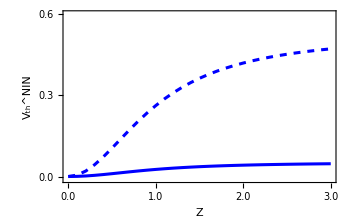

```mathematica
VthnZ01=Import["check100.dat"][[All,{1,3}]];
VthnZ10=Import["check101.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
A0=ListLinePlot[{VthnZ01,VthnZ10},Frame->True,PlotRange->{-0.00000001,0.0000006},Frame->True,FrameLabel->{Style["Z",13.5,Bold,Black],Style["V_th^NIN",13.5,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,11],FrameTicks->{{{{0.0000003,"0.3"},{0.0000006,"0.6"},{0.000002,"0.2"},{-0.0000002,"-0.2"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.2],Opacity[1],Blue],Directive[AbsoluteThickness[2.2],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15]]
```

# Thermovoltage (V_th^NIS) in NIS setup with Barrier strength (Z)(ΔT=(0.1, 1),T2=3)

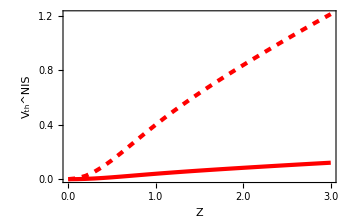

```mathematica
VthsZ01=Import["check100.dat"][[All,{1,2}]];
VthsZ10=Import["check101.dat"][[All,{1,2}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{VthsZ01,VthsZ10},Frame->True,PlotRange->All,Frame->True,FrameLabel->{Style["Z",25,Bold,Black],Style["V_th^NIS",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0000004,"0.4"},{0.0000008,"0.8"},{0.0000012,"1.2"},{-0.0000012,"-0.2"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15]] (*PlotLegends->Placed[{Style["ΔT=0.1K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Left,Top}],*)
```

```mathematica
xyMinMax={{0.2,1.001},{-.2,0.5}};


ListLinePlot[{VthsZ01,VthsZ10},Frame->True,PlotRange->{All},Frame->True,FrameLabel->{Style["Z",25,Bold,Black],Style["V_th^NIS",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0000004,"0.4"},{0.0000008,"0.8"},{0.0000012,"1.2"},{-0.0000012,"-0.2"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},ImageSize->390,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[A0,Scaled[{0.17,0.57}],Scaled[{0,0}],1.85],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

ListLinePlot::prng: Value of option PlotRange -> {All} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

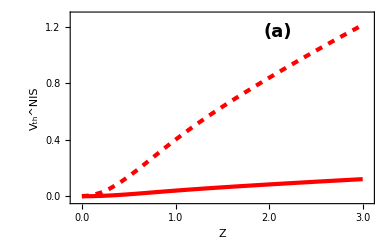

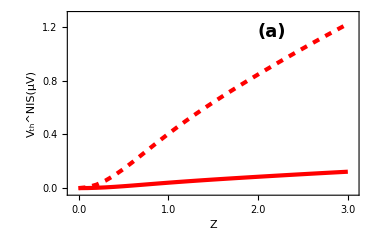

# Delta-T noise in NIN setup for ΔT=(0.1, 1) and T2 = 3 with respect to Z

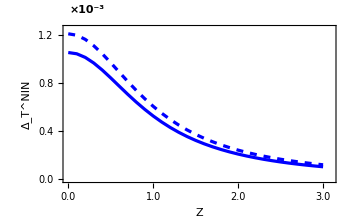

```mathematica
DTnZ01=Import["check100.dat"][[All,{1,5}]];
DTnZ10=Import["check101.dat"][[All,{1,5}]];
Needs["PlotLegends`"]
A2n=ListLinePlot[{DTnZ01,DTnZ10},Frame->True,PlotRange->{{0,3.09},{-0.0000002,0.00125}},Frame->True,FrameLabel->{Style["Z",13.6,Bold,Black],Style["Δ_T^NIN",13.6,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,11],FrameTicks->{{{{0.0004,"0.4"},{0.0008,"0.8"},{0.0012,"1.2"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{77,4},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,11,Bold],Scaled[{0.09,1.1}]]}]
```

# Delta-T noise in NIS setup for ΔT=(0.1, 1) and T2 = 3 with respect to Z

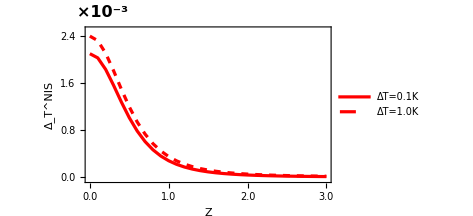

```mathematica
DTsZ01=Import["check100.dat"][[All,{1,4}]];
DTsZ10=Import["check101.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
A2s=ListLinePlot[{DTsZ01,DTsZ10},Frame->True,PlotRange->{-0.00004,0.0025},Frame->True,PlotLegends->Placed[{Style["ΔT=0.1K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",19,Bold,Black],Style["Δ_T^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0016,"1.6"},{0.0008,"0.8"},{0.0024,"2.4"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{79,10},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,16,Bold],Scaled[{0.07,1.09}]]}]
```

```mathematica
xyMinMax={{0.2,1.001},{-.2,0.5}};


ListLinePlot[{DTsZ01,DTsZ10},Frame->True,PlotRange->{{0,3.09},{-0.00004,0.0025}},Frame->True,FrameLabel->{Style["Z",19,Bold,Black],Style["Δ_T^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0016,"1.6"},{0.0008,"0.8"},{0.0024,"2.4"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->370,LabelStyle->Directive[Bold,Black,15],PlotRangeClipping->False,(*Ensure clipping is disabled here*)ImagePadding->{{70,14},{70,35}},(*Placed outside Epilog*)Epilog->{Transparent,Inset[A2n,Scaled[{0.44,0.34}],Scaled[{0,0}],2.5],Text[Style["×\!\(\*SuperscriptBox[\(10\), \(-3\)]\)",Black,16,Bold],Scaled[{0.07,1.09}] (*Adjust this for exact placement*)]}]
```

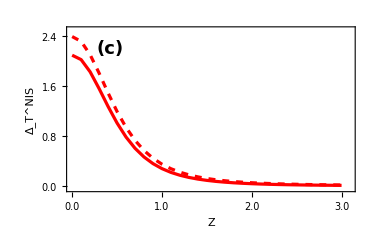

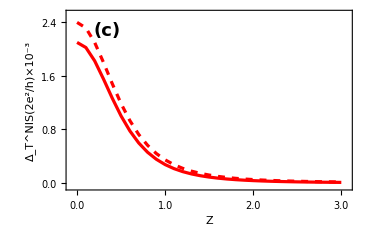

# Ratio of Delta-T noise for NIS and NIN for ΔT=(0.1, 1) and T2 = 3

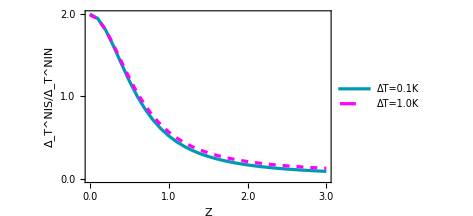

```mathematica
data1=Import["check100.dat"][[All,{1,6}]];
data2=Import["check101.dat"][[All,{1,6}]];
Needs["PlotLegends`"]
A4=ListLinePlot[{data1,data2},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{Style["ΔT=0.1K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",19,Bold,Black],Style["Δ_T^NIS/Δ_T^NIN",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{2.0,"2.0"},{1.0,"1.0"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],RGBColor[0,.6,.7]],Directive[AbsoluteThickness[2.3],Opacity[1],Magenta,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Black,DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15]]
```

# Δ_T thermal noise of NIN for ΔT = 0.1K, 1K for T2 = 3K with respect to Z

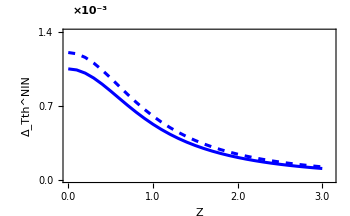

```mathematica
DTthnZ01=Import["check100.dat"][[All,{1,9}]];
DTthnZ10=Import["check101.dat"][[All,{1,9}]];
Needs["PlotLegends`"]
A50=ListLinePlot[{DTthnZ01,DTthnZ10},Frame->True,PlotRange->{{0,3.1},{0,0.0014}},Frame->True,FrameLabel->{Style["Z",13.6,Bold,Black],Style["Δ_Tth^NIN",13.6,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,11],FrameTicks->{{{{0.0007,"0.7"},{0.0014,"1.4"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.2],Opacity[1],Blue],Directive[AbsoluteThickness[2.2],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{75,4},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,11,Bold],Scaled[{0.1,1.12}]]}]
```

# Δ_T thermal noise of NIS for ΔT = 0.1K, 1K for T2 = 3K with respect to Z

```mathematica
DTthsZ01=Import["check100.dat"][[All,{1,7}]];
DTthsZ10=Import["check101.dat"][[All,{1,7}]];
Needs["PlotLegends`"]
A60=ListLinePlot[{DTthsZ01,DTthsZ10},Frame->True,PlotRange->{0,0.0026},Frame->True,PlotLegends->Placed[{Style["ΔT = 0.1K",16,Black,Bold],Style["ΔT = 1K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",19,Bold,Black],Style["Δ_Tth^NIS(2e^2/h)×10^-3",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0013,"1.3"},{0.0026,"2.6"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.2],Opacity[1],Red],Directive[AbsoluteThickness[2.2],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{75,4},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,16,Bold],Scaled[{0.07,1.09}]]}]
```

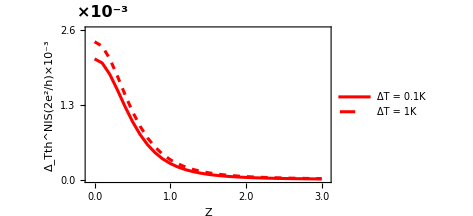

```mathematica
xyMinMax={{0.2,1.001},{-.2,0.5}};


ListLinePlot[{DTthsZ01,DTthsZ10},Frame->True,PlotRange->{{0,3.1},{0,0.0026}},Frame->True,FrameLabel->{Style["Z",19,Bold,Black],Style["Δ_Tth^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0016,"1.6"},{0.0008,"0.8"},{0.0024,"2.4"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->370,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[A50,Scaled[{0.43,0.34}],Scaled[{0,0}],2.4],PlotRange->{0.2,0.3},PlotRangeClipping->False},ImagePadding->{{75,4},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,16,Bold],Scaled[{0.07,1.09}]]}]
```

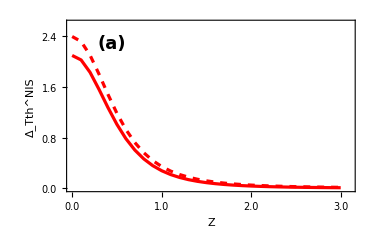

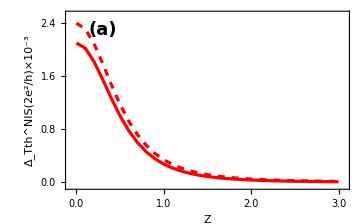

# Δ_T shot noise of NIN for ΔT = 0.1K, 1K for T2 = 3K with respect to Z

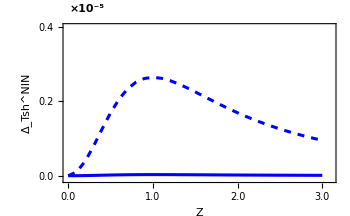

```mathematica
DTshnZ01=Import["check100.dat"][[All,{1,10}]];
DTshnZ10=Import["check101.dat"][[All,{1,10}]];
Needs["PlotLegends`"]
A70=ListLinePlot[{DTshnZ01,DTshnZ10},Frame->True,PlotRange->{{0,3.1},{-0.0000001,0.000004}},Frame->True,FrameLabel->{Style["Z",13.6,Bold,Black],Style["Δ_Tsh^NIN",13,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,11],FrameTicks->{{{{0.00,"0.0"},{2*10^-6,"0.2"},{4*10^-6,"0.4"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},
PlotStyle->{Directive[AbsoluteThickness[2.2],Opacity[1],Blue],Directive[AbsoluteThickness[2.2],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{75,4},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-5",Black,11,Bold],Scaled[{0.09,1.09}]]}]
```

# Δ_T shot noise of NIS for ΔT = 0.1K, 1K for T2 = 3K with respect to Z

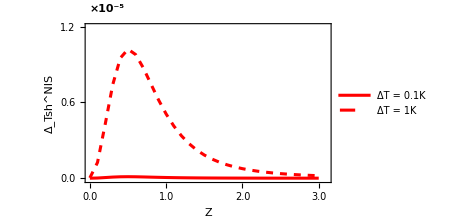

```mathematica
DTshsZ01=Import["check100.dat"][[All,{1,8}]];
DTshsZ10=Import["check101.dat"][[All,{1,8}]];
Needs["PlotLegends`"]
A8=ListLinePlot[{DTshsZ01,DTshsZ10},Frame->True,PlotRange->{{0,3.1},{-0.0000001,0.000012}},Frame->True,PlotLegends->Placed[{Style["ΔT = 0.1K",16,Black,Bold],Style["ΔT = 1K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",19,Bold,Black],Style["Δ_Tsh^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.00,"0.0"},{12*10^-6,"1.2"},{6*10^-6,"0.6"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},
PlotStyle->{Directive[AbsoluteThickness[2.2],Opacity[1],Red],Directive[AbsoluteThickness[2.2],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{75,4},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-5",Black,11,Bold],Scaled[{0.09,1.09}]]}]
```

```mathematica
xyMinMax={{0.2,1.001},{-.2,0.5}};


ListLinePlot[{DTshsZ01,DTshsZ10},Frame->True,PlotRange->{{0,3.09},{-0.0000002,12*10^-6}},Frame->True,FrameLabel->{Style["Z",19,Bold,Black],Style["Δ_Tsh^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.00,"0.0"},{12*10^-6,"1.2"},{6*10^-6,"0.6"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},
PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->370,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[A70,Scaled[{0.5,0.45}],Scaled[{0,0}],2.1],PlotRange->{0.2,0.3},PlotRangeClipping->False},ImagePadding->{{70,4},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-5",Black,16,Bold],Scaled[{0.07,1.09}]]}]
```

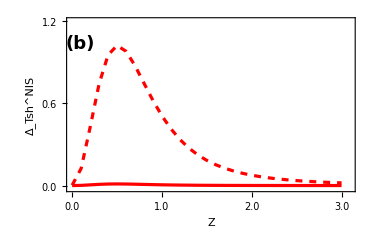

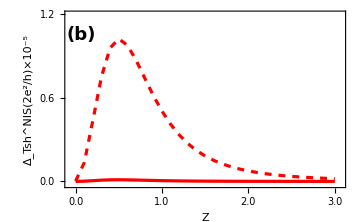

# Calculation of Delta-T noise for NIN and NIS at different Z values Z = 0, 1, 3 as a function of temperature bias

```mathematica
T1=T;
T2=3;
Z=3;
A=-(2 k1 (q1+q2) u0^2 v0)/((q1+q2) u0 v0^2 (-k1+q2-2 ⅈ Z)+u0 (-u0^2 (k1+q1+2 ⅈ Z)+v0^2 (k1-q2+2 ⅈ Z)) (k2+q2-2 ⅈ Z));

(* -(2 k1 (q1+q2) u0^2 v0)/((q1+q2) u0 v0^2 (-k1+q2-2 ⅈ Z)+u0 (-u0^2 (k1+q1+2 ⅈ Z)+v0^2 (k1-q2+2 ⅈ Z)) (k2+q2-2 ⅈ Z)) *)

B=(-ⅈ (k1-q1) (k2+q2) u0^2+ⅈ (k2-q1) (k1+q2) v0^2-2 (k1+k2-q1+q2) (u0-v0) (u0+v0) Z+4 ⅈ (u0-v0) (u0+v0) Z^2)/(-ⅈ (k1+q1) (k2+q2) u0^2+ⅈ (k2-q1) (k1-q2) v0^2-2 (k1-k2+q1-q2) (u0-v0) (u0+v0) Z-4 ⅈ (u0-v0) (u0+v0) Z^2);
u0=Piecewise[{{(1/2*(1+I((-G^2+ds^2)/G^2)^(1/2)))^(1/2),G^2< ds^2},{(1/2*(1+((G^2-ds^2)/G^2)^(1/2)))^(1/2),G^2> ds^2 }}];

v0=Piecewise[{{(1/2*(1-I((-G^2+ds^2)/G^2)^(1/2)))^(1/2),G^2< ds^2},{(1/2*(1-((G^2-ds^2)/G^2)^(1/2)))^(1/2),G^2> ds^2 }}]; 

q1=Piecewise[{{(1+(I*(-G^2+ds^2)^(1/2))/Ef)^(1/2),G^2< ds^2},{(1+((G^2-ds^2)^(1/2))/Ef)^(1/2),G^2> ds^2 }}];

q2=Piecewise[{{(1-(I*(-G^2+ds^2)^(1/2))/Ef)^(1/2),G^2< ds^2},{(1-((G^2-ds^2)^(1/2))/Ef)^(1/2),G^2> ds^2 }}]; 
k1=Piecewise[{{Sqrt[1+G/Ef],G>=Ef},{Sqrt[1-G/Ef],G<Ef}}];
k2=Piecewise[{{Sqrt[1+G/Ef],G>=Ef},{Sqrt[1-G/Ef],G<Ef}}];
Bn=k1^2/(k1^2+Z^2);
kb=1;
Tc=9.2; 
d=1.764*kb*Tc;  
Ef=100*d;
ds=d;
a1=kb*T2;
df=Exp[(G)/(a1)]/((Exp[(G)/(a1)]+1)^2 a1);
SetSharedVariable[list1]
list1={};
ParallelDo[{
L1=NIntegrate[(1+Abs[A]^2-Abs[B]^2)*(G)*df,{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->100]/T2;
G1=NIntegrate[(1+Abs[A]^2-Abs[B]^2)*df,{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->100];
L2=NIntegrate[(Bn)*(G)*df,{G,-1000,1000},Method->"GlobalAdaptive",MaxRecursion->100]/T2;
G2=NIntegrate[(Bn)*df,{G,-1000,1000},Method->"GlobalAdaptive",MaxRecursion->100];
Vth1=(-L1*(T1-T2))/G1;
Vth2=(-L2*(T1-T2))/G2;
f11=1/(1+Exp[(G-Vth1)/(kb*T1)]);
f12=1/(1+Exp[(G-Vth2)/(kb*T1)]);
f2=1/(1+Exp[G/(kb*T2)]);Q11NSth=NIntegrate[(1-Abs[B]^2+Abs[A]^2)(f11(1-f11) +f2(1-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->10];
Q11NSsh=NIntegrate[(Abs[B]^2(1-Abs[B]^2)+Abs[A]^2(1-Abs[A]^2)+2Abs[A]^2*Abs[B]^2)(f11-f2)^2,{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->10];
Q11NS=Q11NSth+Q11NSsh;
Q11NNth=NIntegrate[Bn(f12(1-f12) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Q11NNsh=NIntegrate[Bn(1-Bn)(f12-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Q11NN=Q11NNth+Q11NNsh;
list=AppendTo[list1,{T,Re[Vth1]8.617*10^-5,Re[Vth2]8.617*10^-5,2*Re[Q11NS]*8.617*10^-5,2*Re[Q11NN]*8.617*10^-5,Re[Q11NS]/Re[Q11NN],2*Q11NSth*8.617*10^-5,2*Q11NSsh*8.617*10^-5,2*Q11NNth*8.617*10^-5,2*Q11NNsh*8.617*10^-5}];
},{T,3,5,0.1}];//AbsoluteTiming
listn=Sort[list1];
Export["check202.dat",listn]
```

{28.5153,Null}

check202.dat

# Thermovoltage (V_th^NIN) in NIN setup with Barrier strength (Z=0, 1, 3) and T2=3 with temperature bias ΔT

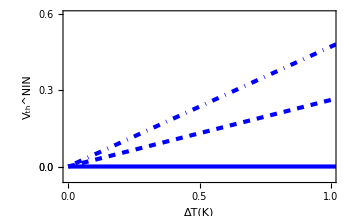

```mathematica
VthnT0=Import["check200.dat"][[All,{1,3}]];
VthnT1=Import["check201.dat"][[All,{1,3}]];
VthnT3=Import["check202.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
A1t=ListLinePlot[{VthnT0,VthnT1,VthnT3},Frame->True,PlotRange->{{3,4},{-0.00000005,0.0000006}},Frame->True,FrameLabel->{Style["ΔT(K)",13,Bold,Black],Style["V_th^NIN",13.8,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,11],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},FrameTicks->{{{{0.0000003,"0.3"},{0.0000006,"0.6"},{0.000000,"0.0"},{-0.0000002,"-0.2"},{0,"0.0"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->350,LabelStyle->Directive[Bold,Black,15]]
```

# Thermovoltage (V_th^NIS) in NIS setup with Barrier strength (Z=0, 1, 3) and T2=3 with temperature bias ΔT

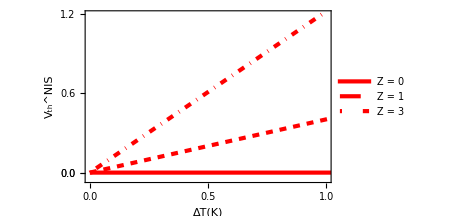

```mathematica
VthsT0=Import["check200.dat"][[All,{1,2}]];
VthsT1=Import["check201.dat"][[All,{1,2}]];
VthsT3=Import["check202.dat"][[All,{1,2}]];
Needs["PlotLegends`"]
A1st=ListLinePlot[{VthsT0,VthsT1,VthsT3},Frame->True,PlotRange->{{3,4},{-0.00000005,0.0000012}},Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Left,Top}],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["V_th^NIS",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},FrameTicks->{{{{0.0000006,"0.6"},{0.0000012,"1.2"},{0.000000,"0.0"},{-0.0000002,"-0.2"},{0,"0.0"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->350,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
xyMinMax={{0.2,1.001},{-.2,0.5}};


ListLinePlot[{VthsT0,VthsT1,VthsT3},Frame->True,PlotRange->{{3,4},{-0.00000005,0.0000014}},Frame->True,FrameLabel->{Style["ΔT(K)",20,Bold,Black],Style["V_th^NIS",20,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},FrameTicks->{{{{0.0000006,"0.6"},{0.0000012,"1.2"},{0.000000,"0.0"},{-0.0000002,"-0.2"},{0,"0.0"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->360,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[A1t,Scaled[{0.185,0.57}],Scaled[{0,0}],.6],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

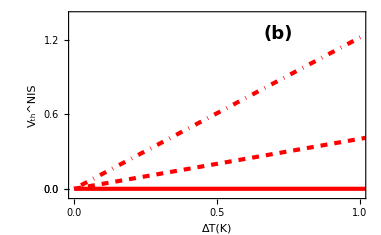

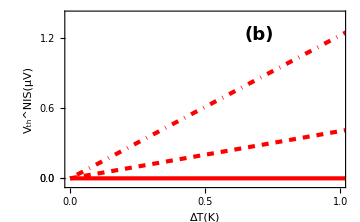

# Delta-T noise in NIN setup for Z = (0, 1, 3) and T2 = 3 with respect to ΔT

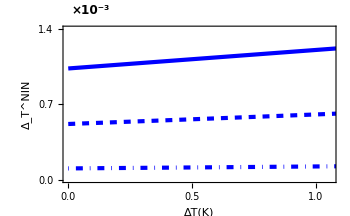

```mathematica
DTnT0=Import["check200.dat"][[All,{1,5}]];
DTnT1=Import["check201.dat"][[All,{1,5}]];
DTnT3=Import["check202.dat"][[All,{1,5}]];
Needs["PlotLegends`"]
A1Dn=ListLinePlot[{DTnT0,DTnT1,DTnT3},Frame->True,PlotRange->{{3,4.06},{0.000,0.0014}},Frame->True,FrameLabel->{Style["ΔT(K)",12.5,Bold,Black],Style["Δ_T^NIN",13,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,11],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.0007,"0.7"},{0.0014,"1.4"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{77,2},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,12,Bold],Scaled[{0.1,1.1}]]}]
```

# Delta-T noise in NIS setup for Z = (0, 1, 3) and T2 = 3 with respect to ΔT

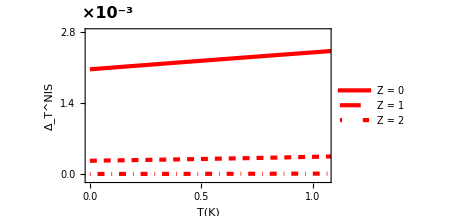

```mathematica
DTsT0=Import["check200.dat"][[All,{1,4}]];
DTsT1=Import["check201.dat"][[All,{1,4}]];
DTsT3=Import["check202.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
A1Ds=ListLinePlot[{DTsT0,DTsT1,DTsT3},Frame->True,PlotRange->{{3,4.06},{-0.0001,0.0028}},Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 2"},{Center,Center}],FrameLabel->{Style["T(K)",25,Bold,Black],Style["Δ_T^NIS",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.0014,"1.4"},{0.0028,"2.8"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{77,4},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,16,Bold],Scaled[{0.09,1.1}]]}]
```

```mathematica
xyMinMax={{0.2,1.001},{-.2,0.5}};


ListLinePlot[{DTsT0,DTsT1,DTsT3},Frame->True,PlotRange->{{3,4.07},{-0.0001,0.0026}},Frame->True,FrameLabel->{Style["T(K)",21,Bold,Black],Style["Δ_T^NIS",21,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.0013,"1.3"},{0.0026,"2.6"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->370,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[A1Dn,Scaled[{0.51,0.36}],Scaled[{0,0}],.69],PlotRange->{0.2,0.3},PlotRangeClipping->False},ImagePadding->{{70,2},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,11,Bold],Scaled[{0.09,1.1}]]}]
```

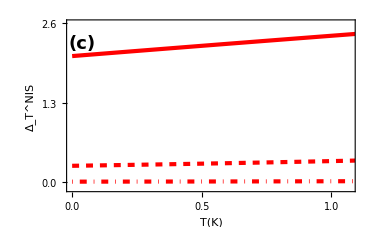

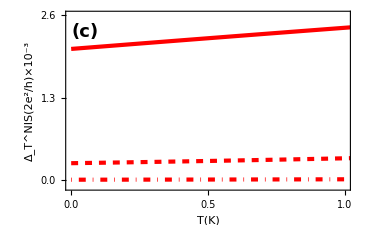

# Ratio of Delta-T noise for NIS and NIN for ΔT and T2 = 3

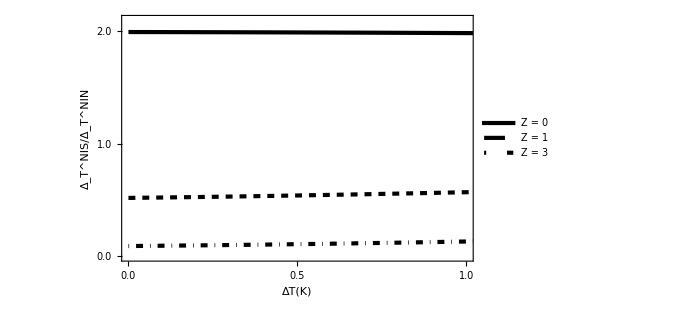

```mathematica
data1=Import["check200.dat"][[All,{1,6}]];
data2=Import["check201.dat"][[All,{1,6}]];
data3=Import["check202.dat"][[All,{1,6}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->{{3,4},{0.000,2.1}},Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Center,Center}],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["Δ_T^NIS/Δ_T^NIN",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Black,Dashed],Directive[AbsoluteThickness[3],Opacity[1],Black,DotDashed]},FrameTicks->{{{{0.000,"0.0"},{1.0,"1.0"},{2,"2.0"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->350,LabelStyle->Directive[Bold,Black,15]]
```

# Comparison of Δ_T thermal noise of NIN for Z = 0, 1, 3 for T2 = 3K with respect to ΔT

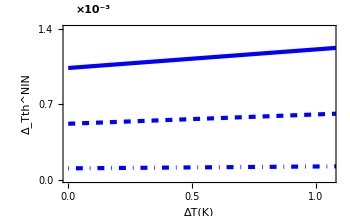

```mathematica
DTthnT0=Import["check200.dat"][[All,{1,9}]];
DTthnT1=Import["check201.dat"][[All,{1,9}]];
DTthnT3=Import["check202.dat"][[All,{1,9}]];
Needs["PlotLegends`"]
ADtn=ListLinePlot[{DTthnT0,DTthnT1,DTthnT3},Frame->True,PlotRange->{{3,4.06},{0.000,0.0014}},Frame->True,FrameLabel->{Style["ΔT(K)",12,Bold,Black],Style["Δ_Tth^NIN",13,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,11],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.0007,"0.7"},{0.0014,"1.4"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{77,2},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,11,Bold],Scaled[{0.11,1.1}]]}]
```

# Comparison of Δ_T shot noise of NIN for Z = 0, 1, 3 for T2 = 3K with respect to ΔT

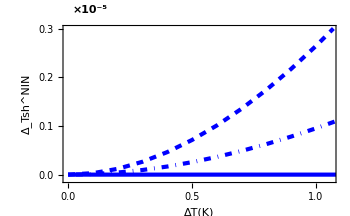

```mathematica
DTshnT0=Import["check200.dat"][[All,{1,10}]];
DTshnT1=Import["check201.dat"][[All,{1,10}]];
DTshnT3=Import["check202.dat"][[All,{1,10}]];
Needs["PlotLegends`"]
ADsn=ListLinePlot[{DTshnT0,DTshnT1,DTshnT3},Frame->True,PlotRange->{{3,4.06},{-0.0000001,0.000003}},Frame->True,FrameLabel->{Style["ΔT(K)",13,Bold,Black],Style["Δ_Tsh^NIN",13,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,11],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.000001,"0.1"},{0.000002,"0.2"},{0.000003,"0.3"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{77,2},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-5",Black,11,Bold],Scaled[{0.1,1.1}]]}]
```

# Comparison of Δ_T thermal noise of NIS for Z = 0, 1, 3 for T2 = 3K with respect to ΔT

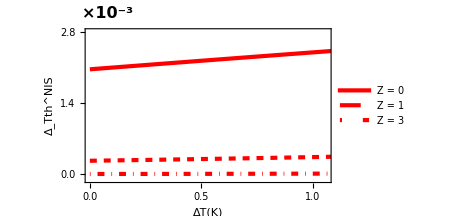

```mathematica
DTthsT0=Import["check200.dat"][[All,{1,7}]];
DTthsT1=Import["check201.dat"][[All,{1,7}]];
DTthsT3=Import["check202.dat"][[All,{1,7}]];
Needs["PlotLegends`"]
A1s=ListLinePlot[{DTthsT0,DTthsT1,DTthsT3},Frame->True,PlotRange->{{3,4.06},{-0.0001,0.0028}},Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Center,Center}],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["Δ_Tth^NIS",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.0014,"1.4"},{0.0028,"2.8"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{77,4},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,16,Bold],Scaled[{0.09,1.1}]]}]
```

```mathematica
xyMinMax={{0.2,1.001},{-.2,0.5}};


ListLinePlot[{DTthsT0,DTthsT1,DTthsT3},Frame->True,PlotRange->{{3,4.06},{-0.0001,0.0028}},Frame->True,FrameLabel->{Style["ΔT(K)",21,Bold,Black],Style["Δ_Tth^NIS",21,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.0014,"1.4"},{0.0028,"2.8"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->370,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[ADtn,Scaled[{0.51,0.36}],Scaled[{0,0}],.68],PlotRange->{0.2,0.3},PlotRangeClipping->False},ImagePadding->{{77,3},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,11,Bold],Scaled[{0.1,1.1}]]}]
```

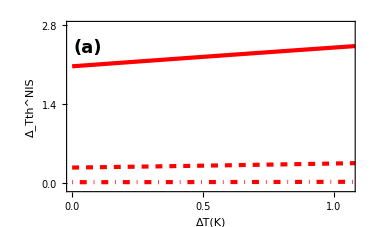

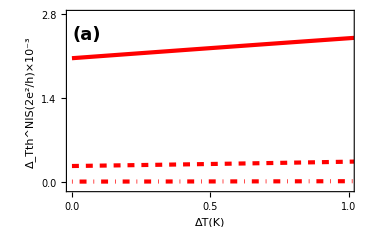

# Comparison of Δ_T shot noise of NIS for Z = 0, 1, 3 for T2 = 3K with respect to ΔT

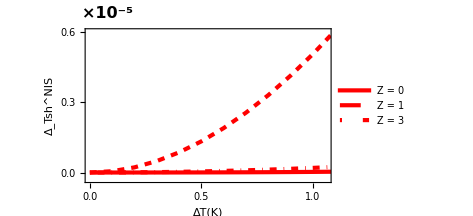

```mathematica
DTshsT0=Import["check200.dat"][[All,{1,8}]];
DTshsT1=Import["check201.dat"][[All,{1,8}]];
DTshsT3=Import["check202.dat"][[All,{1,8}]];
Needs["PlotLegends`"]
ADss=ListLinePlot[{DTshsT0,DTshsT1,DTshsT3},Frame->True,PlotRange->{{3,4.06},{-0.0000003,0.000006}},Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Center,Center}],FrameLabel->{Style["ΔT(K)",22,Bold,Black],Style["Δ_Tsh^NIS",22,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.000003,"0.3"},{0.000006,"0.6"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{70,2},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-5",Black,16,Bold],Scaled[{0.09,1.1}]]}]
```

```mathematica
xyMinMax={{0.2,1.001},{-.2,0.5}};


ListLinePlot[{DTshsT0,DTshsT1,DTshsT3},Frame->True,PlotRange->{{3,4.06},{-0.0000003,0.000006}},Frame->True,FrameLabel->{Style["ΔT(K)",21,Bold,Black],Style["Δ_Tsh^NIS",21,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.000003,"0.3"},{0.000006,"0.6"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->370,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[ADsn,Scaled[{0.18,0.475}],Scaled[{0,0}],.74],PlotRange->{0.2,0.3},PlotRangeClipping->False},ImagePadding->{{70,2},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,16,Bold],Scaled[{0.09,1.1}]]}]
```

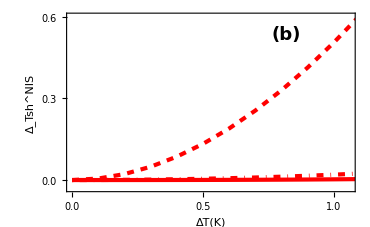

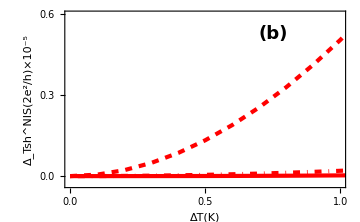

# Quantum Noise NIN and NIS for T1 = 3.1K and 4K, T2 = 3K as a function of Z for applied voltage bias V = 0.0001

```mathematica
T1=4;
T2=3;
A=-((2 k1 (q1+q2) u0^2 v0)/((q1+q2) u0 v0^2 (-k1+q2-2 ⅈ Z)+u0 (-u0^2 (k1+q1+2 ⅈ Z)+v0^2 (k1-q2+2 ⅈ Z)) (k2+q2-2 ⅈ Z)));

(* -(2 k1 (q1+q2) u0^2 v0)/((q1+q2) u0 v0^2 (-k1+q2-2 ⅈ Z)+u0 (-u0^2 (k1+q1+2 ⅈ Z)+v0^2 (k1-q2+2 ⅈ Z)) (k2+q2-2 ⅈ Z)) *)

B=(-ⅈ (k1-q1) (k2+q2) u0^2+ⅈ (k2-q1) (k1+q2) v0^2-2 (k1+k2-q1+q2) (u0-v0) (u0+v0) Z+4 ⅈ (u0-v0) (u0+v0) Z^2)/(-ⅈ (k1+q1) (k2+q2) u0^2+ⅈ (k2-q1) (k1-q2) v0^2-2 (k1-k2+q1-q2) (u0-v0) (u0+v0) Z-4 ⅈ (u0-v0) (u0+v0) Z^2);
u0=Piecewise[{{(1/2*(1+I((-G^2+ds^2)/G^2)^(1/2)))^(1/2),G^2< ds^2},{(1/2*(1+((G^2-ds^2)/G^2)^(1/2)))^(1/2),G^2> ds^2 }}];

v0=Piecewise[{{(1/2*(1-I((-G^2+ds^2)/G^2)^(1/2)))^(1/2),G^2< ds^2},{(1/2*(1-((G^2-ds^2)/G^2)^(1/2)))^(1/2),G^2> ds^2 }}]; 

q1=Piecewise[{{(1+(I*(-G^2+ds^2)^(1/2))/Ef)^(1/2),G^2< ds^2},{(1+((G^2-ds^2)^(1/2))/Ef)^(1/2),G^2> ds^2 }}];

q2=Piecewise[{{(1-(I*(-G^2+ds^2)^(1/2))/Ef)^(1/2),G^2< ds^2},{(1-((G^2-ds^2)^(1/2))/Ef)^(1/2),G^2> ds^2 }}]; 
k1=Piecewise[{{Sqrt[1+G/Ef],G>=Ef},{Sqrt[1-G/Ef],G<Ef}}];
k2=Piecewise[{{Sqrt[1+G/Ef],G>=Ef},{Sqrt[1-G/Ef],G<Ef}}];
Bn=k1^2/(k1^2+Z^2);
kb=8.617*10^-5;
Tc=9.2; 
d=1.764*kb*Tc;  
Ef=100*d;
ds=d;
a1=kb*T2;
df=Exp[(G)/(a1)]/((Exp[(G)/(a1)]+1)^2 a1);
SetSharedVariable[list1]
list1={};
ParallelDo[{V1=0.0001;
f11=1/(1+Exp[(G-V1)/(kb*T1)]);
f12=1/(1+Exp[(G-V1)/(kb*T1)]);
f2=1/(1+Exp[G/(kb*T2)]);
Qth11NS=NIntegrate[(1-Abs[B]^2+Abs[A]^2)(f11(1-f11) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qsh11NS=NIntegrate[(Abs[B]^2(1-Abs[B]^2)+Abs[A]^2(1-Abs[A]^2)+2Abs[A]^2*Abs[B]^2)(f11-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qth11NN=NIntegrate[Bn(f12(1-f12) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qsh11NN=NIntegrate[Bn(1-Bn)(f12-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
list=AppendTo[list1,{Z,2*Re[Qth11NS],2*Re[Qsh11NS],(2*Re[Qth11NS]+2*Re[Qsh11NS]),2*Re[Qth11NN],2*Re[Qsh11NN],(2*Re[Qth11NN]+2*Re[Qsh11NN]),(2*Re[Qsh11NS]+2*Re[Qth11NS])/(2*Re[Qsh11NN]+2*Re[Qth11NN])}];
},{Z,0.0,3.0,0.1}];//AbsoluteTiming
listn=Sort[list1];
Export["QT1.dat",listn]
```

{30.3559,Null}

QT1.dat

# Quantum noise correlation for NIN as a function of Z

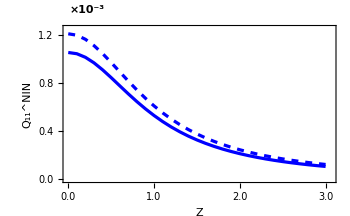

```mathematica
dataQn0=Import["QT1.dat"][[All,{1,7}]];
dataQn1=Import["QT01.dat"][[All,{1,7}]];
Needs["PlotLegends`"]
AQn=ListLinePlot[{dataQn0,dataQn1},Frame->True,PlotRange->{{0,3.06},{-0.000002,0.00125}},Frame->True,FrameLabel->{Style["Z",13,Bold,Black],Style["Q_11^NIN",13,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,11],FrameTicks->{{{{0.0004,"0.4"},{0.0008,"0.8"},{0.0012,"1.2"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{75,6},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,11,Bold],Scaled[{0.09,1.1}]]}]
```

# Quantum Thermal noise of NIN as a function of Z

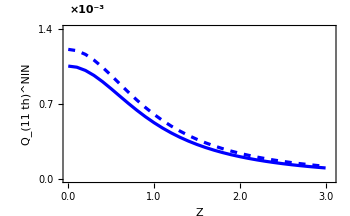

```mathematica
dataQnt0=Import["QT1.dat"][[All,{1,5}]];
dataQnt1=Import["QT01.dat"][[All,{1,5}]];
Needs["PlotLegends`"]
AQnt=ListLinePlot[{dataQnt0,dataQnt1},Frame->True,PlotRange->{{0,3.06},{-0.000002,0.0014}},Frame->True,FrameLabel->{Style["Z",13,Bold,Black],Style["Q_(11  th)^NIN",13,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,11],FrameTicks->{{{{0.0007,"0.7"},{0.0014,"1.4"},{0.0026,"2.6"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{77,6},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,11,Bold],Scaled[{0.09,1.1}]]}]
```

# Quantum Shot noise of NIN as function of Z

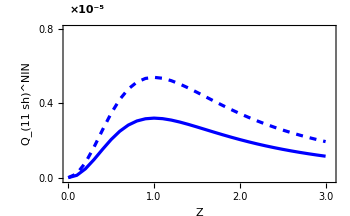

```mathematica
dataQns0=Import["QT1.dat"][[All,{1,6}]];
dataQns1=Import["QT01.dat"][[All,{1,6}]];
Needs["PlotLegends`"]
AQns=ListLinePlot[{dataQns0,dataQns1},Frame->True,PlotRange->{{0,3.06},{-0.0000001,0.000008}},Frame->True,FrameLabel->{Style["Z",13,Bold,Black],Style["Q_(11  sh)^NIN",12.5,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,11],FrameTicks->{{{{0.0004,"0.4"},{0.000004,"0.4"},{0.000008,"0.8"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{77,6},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-5",Black,11,Bold],Scaled[{0.09,1.1}]]}]
```

# Quantum noise correlation for NIS as a function of Z

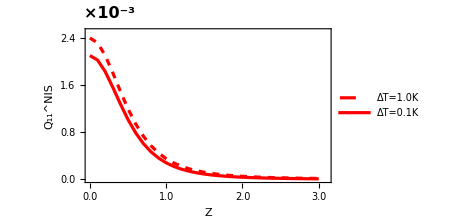

```mathematica
dataQs0=Import["QT1.dat"][[All,{1,4}]];
dataQs1=Import["QT01.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
AQs=ListLinePlot[{dataQs0,dataQs1},Frame->True,PlotRange->{{0,3.1},{-0.000002,0.0025}},Frame->True,PlotLegends->Placed[{Style["ΔT=1.0K",16,Black,Bold],Style["ΔT=0.1K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",19,Bold,Black],Style["Q_11^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0024,"2.4"},{0.0016,"1.6"},{0.0008,"0.8"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{70,2},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,16,Bold],Scaled[{0.1,1.1}]]}]
```

```mathematica
xyMinMax={{0.2,1.001},{-.2,0.5}};


ListLinePlot[{dataQs0,dataQs1},Frame->True,PlotRange->{{0,3.05},{-0.000002,0.0025}},Frame->True,FrameLabel->{Style["Z",20,Bold,Black],Style["Q_11^NIS",20,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0024,"2.4"},{0.0016,"1.6"},{0.0008,"0.8"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->370,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[AQn,Scaled[{0.46,0.42}],Scaled[{0,0}],2.251],PlotRange->{0.2,0.3},PlotRangeClipping->False},ImagePadding->{{79,6},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,16,Bold],Scaled[{0.09,1.1}]]}]
```

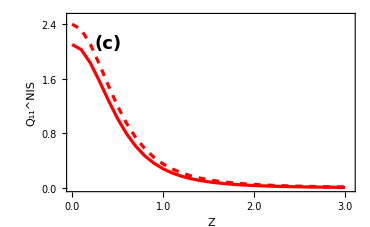

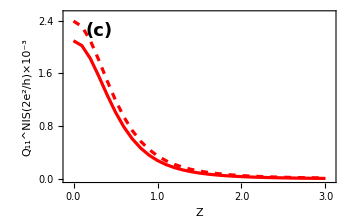

# Quantum Thermal noise of NIS as a function of Z

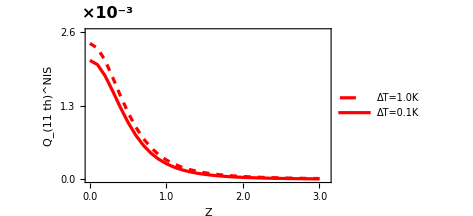

```mathematica
dataQst0=Import["QT1.dat"][[All,{1,2}]];
dataQst1=Import["QT01.dat"][[All,{1,2}]];
Needs["PlotLegends`"]
AQst=ListLinePlot[{dataQst0,dataQst1},Frame->True,PlotRange->{{0,3.09},{-0.000002,0.0026}},Frame->True,PlotLegends->Placed[{Style["ΔT=1.0K",16,Black,Bold],Style["ΔT=0.1K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",19,Bold,Black],Style["Q_(11  th)^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0013,"1.3"},{0.0026,"2.6"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{70,6},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,16,Bold],Scaled[{0.09,1.1}]]}]
```

```mathematica
xyMinMax={{0.2,1.001},{-.2,0.5}};


ListLinePlot[{dataQst0,dataQst1},Frame->True,PlotRange->{{0,3.09},{-0.000002,0.0025}},Frame->True,FrameLabel->{Style["Z",20,Bold,Black],Style["Q_(11  th)^NIS",20,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0024,"2.4"},{0.0016,"1.6"},{0.0008,"0.8"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->370,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[AQnt,Scaled[{0.45,0.4}],Scaled[{0,0}],2.37],PlotRange->{0.2,0.3},PlotRangeClipping->False},ImagePadding->{{70,6},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,16,Bold],Scaled[{0.09,1.1}]]}]
```

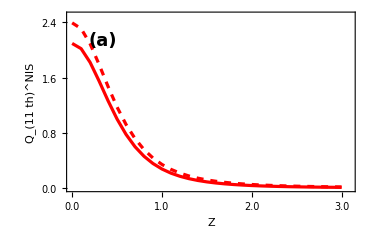

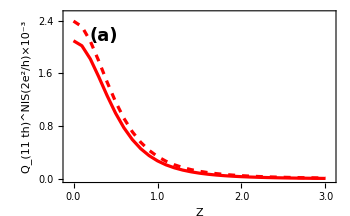

# Quantum Shot noise of NIS as function of Z

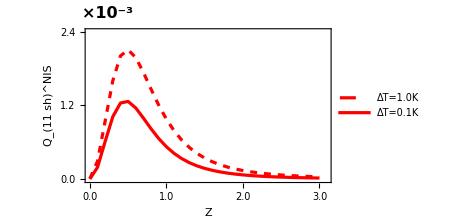

```mathematica
dataQss0=Import["QT1.dat"][[All,{1,3}]];
dataQss1=Import["QT01.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
AQss=ListLinePlot[{dataQss0,dataQss1},Frame->True,PlotRange->{{0,3.09},{-0.0000001,0.000024}},Frame->True,PlotLegends->Placed[{Style["ΔT=1.0K",16,Black,Bold],Style["ΔT=0.1K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",19,Bold,Black],Style["Q_(11  sh)^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0004,"0.4"},{0.000012,"1.2"},{0.000024,"2.4"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{70,2},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,16,Bold],Scaled[{0.09,1.1}]]}]
```

```mathematica
xyMinMax={{0.2,1.001},{-.2,0.5}};


ListLinePlot[{dataQss0,dataQss1},Frame->True,PlotRange->{{0,3.06},{-0.0000001,0.000024}},Frame->True,FrameLabel->{Style["Z",19,Bold,Black],Style["Q_(11  sh)^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0004,"0.4"},{0.000012,"1.2"},{0.000024,"2.4"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->370,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[AQns,Scaled[{0.5,0.45}],Scaled[{0,0}],2.25],PlotRange->{0.2,0.3},PlotRangeClipping->False},ImagePadding->{{77,6},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,11,Bold],Scaled[{0.09,1.1}]]}]
```

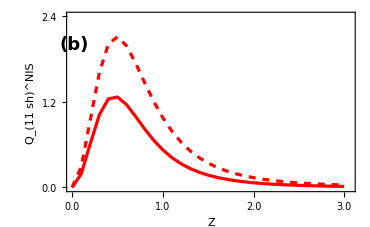

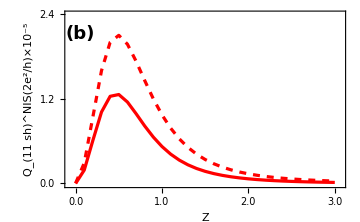

# Ratio of Quantum noise in NIS and NIN as a function of Z

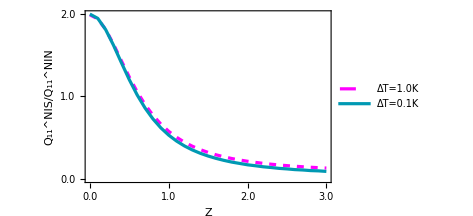

```mathematica
dataQn0=Import["QT1.dat"][[All,{1,8}]];
dataQn1=Import["QT01.dat"][[All,{1,8}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{dataQn0,dataQn1},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{Style["ΔT=1.0K",16,Black,Bold],Style["ΔT=0.1K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",19,Bold,Black],Style["Q_11^NIS/Q_11^NIN",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{2.0,"2.0"},{1.0,"1.0"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Magenta,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],RGBColor[0,.6,.7]],Directive[AbsoluteThickness[2.3],Opacity[1],Black,DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15]]
```

# Quantum Noise NIN and NIS for Z = 0, 1, 3, T2 = 3K as a function of ΔT for applied voltage bias V = 0.0001

```mathematica
T1=T;
T2=3;
Z=3;
A=-((2 k1 (q1+q2) u0^2 v0)/((q1+q2) u0 v0^2 (-k1+q2-2 ⅈ Z)+u0 (-u0^2 (k1+q1+2 ⅈ Z)+v0^2 (k1-q2+2 ⅈ Z)) (k2+q2-2 ⅈ Z)));

(* -(2 k1 (q1+q2) u0^2 v0)/((q1+q2) u0 v0^2 (-k1+q2-2 ⅈ Z)+u0 (-u0^2 (k1+q1+2 ⅈ Z)+v0^2 (k1-q2+2 ⅈ Z)) (k2+q2-2 ⅈ Z)) *)

B=(-ⅈ (k1-q1) (k2+q2) u0^2+ⅈ (k2-q1) (k1+q2) v0^2-2 (k1+k2-q1+q2) (u0-v0) (u0+v0) Z+4 ⅈ (u0-v0) (u0+v0) Z^2)/(-ⅈ (k1+q1) (k2+q2) u0^2+ⅈ (k2-q1) (k1-q2) v0^2-2 (k1-k2+q1-q2) (u0-v0) (u0+v0) Z-4 ⅈ (u0-v0) (u0+v0) Z^2);
u0=Piecewise[{{(1/2*(1+I((-G^2+ds^2)/G^2)^(1/2)))^(1/2),G^2< ds^2},{(1/2*(1+((G^2-ds^2)/G^2)^(1/2)))^(1/2),G^2> ds^2 }}];

v0=Piecewise[{{(1/2*(1-I((-G^2+ds^2)/G^2)^(1/2)))^(1/2),G^2< ds^2},{(1/2*(1-((G^2-ds^2)/G^2)^(1/2)))^(1/2),G^2> ds^2 }}]; 

q1=Piecewise[{{(1+(I*(-G^2+ds^2)^(1/2))/Ef)^(1/2),G^2< ds^2},{(1+((G^2-ds^2)^(1/2))/Ef)^(1/2),G^2> ds^2 }}];

q2=Piecewise[{{(1-(I*(-G^2+ds^2)^(1/2))/Ef)^(1/2),G^2< ds^2},{(1-((G^2-ds^2)^(1/2))/Ef)^(1/2),G^2> ds^2 }}]; 
k1=Piecewise[{{Sqrt[1+G/Ef],G>=Ef},{Sqrt[1-G/Ef],G<Ef}}];
k2=Piecewise[{{Sqrt[1+G/Ef],G>=Ef},{Sqrt[1-G/Ef],G<Ef}}];
Bn=k1^2/(k1^2+Z^2);
kb=8.617*10^-5;
Tc=9.2; 
d=1.764*kb*Tc;  
Ef=100*d;
ds=d;
a1=kb*T2;
df=Exp[(G)/(a1)]/((Exp[(G)/(a1)]+1)^2 a1);
SetSharedVariable[list1]
list1={};
ParallelDo[{V1=0.0001;
f11=1/(1+Exp[(G-V1)/(kb*T1)]);
f12=1/(1+Exp[(G-V1)/(kb*T1)]);
f2=1/(1+Exp[G/(kb*T2)]);
Qth11NS=NIntegrate[(1-Abs[B]^2+Abs[A]^2)(f11(1-f11) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qsh11NS=NIntegrate[(Abs[B]^2(1-Abs[B]^2)+Abs[A]^2(1-Abs[A]^2)+2Abs[A]^2*Abs[B]^2)(f11-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qth11NN=NIntegrate[Bn(f12(1-f12) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qsh11NN=NIntegrate[Bn(1-Bn)(f12-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
list=AppendTo[list1,{T,2*Re[Qth11NS],2*Re[Qsh11NS],(2*Re[Qth11NS]+2*Re[Qsh11NS]),2*Re[Qth11NN],2*Re[Qsh11NN],(2*Re[Qth11NN]+2*Re[Qsh11NN]),(2*Re[Qsh11NS]+2*Re[Qth11NS])/(2*Re[Qsh11NN]+2*Re[Qth11NN])}];
},{T,3,4.0,0.1}];//AbsoluteTiming
listn=Sort[list1];
Export["check302.dat",listn]
```

{10.3774,Null}

check302.dat

```mathematica
Import["check300.dat"]
```

{{3.,0.00206226,1.5904×10^-9,0.00206226,0.00103404,0.,0.00103404,1.99438},{3.1,0.00209603,1.88325×10^-9,0.00209603,0.00105127,0.,0.00105127,1.9938},{3.2,0.00212969,2.50815×10^-9,0.00212969,0.00106851,0.,0.00106851,1.99314},{3.3,0.00216323,3.56234×10^-9,0.00216323,0.00108574,0.,0.00108574,1.9924},{3.4,0.00219664,5.15751×10^-9,0.00219664,0.00110298,0.,0.00110298,1.99156},{3.5,0.00222992,7.41971×10^-9,0.00222993,0.00112021,0.,0.00112021,1.99063},{3.6,0.00226306,1.04891×10^-8,0.00226307,0.00113744,0.,0.00113744,1.98961},{3.7,0.00229605,1.45191×10^-8,0.00229606,0.00115468,0.,0.00115468,1.98849},{3.8,0.00232889,1.96761×10^-8,0.00232891,0.00117191,0.,0.00117191,1.98727},{3.9,0.00236156,2.61382×10^-8,0.00236159,0.00118915,0.,0.00118915,1.98595},{4.,0.00239407,3.40939×10^-8,0.00239411,0.00120638,0.,0.00120638,1.98454}}

# Quantum noise in NIN setup for Z = (0, 1, 3) and T2 = 3 with respect to ΔT

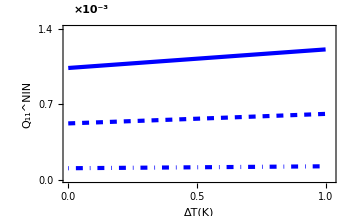

```mathematica
dataQn0T=Import["check300.dat"][[All,{1,7}]];
dataQn1T=Import["check301.dat"][[All,{1,7}]];
dataQn3T=Import["check302.dat"][[All,{1,7}]];
Needs["PlotLegends`"]
AQnT1=ListLinePlot[{dataQn0T,dataQn1T,dataQn3T},Frame->True,PlotRange->{{3,4.02},{0.000,0.0014}},Frame->True,FrameLabel->{Style["ΔT(K)",13,Bold,Black],Style["Q_11^NIN",13,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,11],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.0007,"0.7"},{0.0014,"1.4"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{77,7},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,11,Bold],Scaled[{0.105,1.1}]]}]
```

# Quantum thermal noise in NIN setup for Z = (0, 1, 3) and T2 = 3 with respect to ΔT

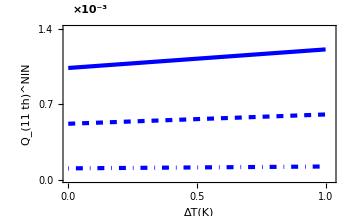

```mathematica
dataQn0Th=Import["check300.dat"][[All,{1,5}]];
dataQn1Th=Import["check301.dat"][[All,{1,5}]];
dataQn3Th=Import["check302.dat"][[All,{1,5}]];
Needs["PlotLegends`"]
AQnTh=ListLinePlot[{dataQn0Th,dataQn1Th,dataQn3Th},Frame->True,PlotRange->{{3,4.02},{0.000,0.0014}},Frame->True,FrameLabel->{Style["ΔT(K)",13,Bold,Black],Style["Q_(11  th)^NIN",13,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,11],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.0007,"0.7"},{0.0014,"1.4"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{77,6},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,11,Bold],Scaled[{0.1,1.1}]]}]
```

# Quantum shot noise in NIN setup for Z = (0, 1, 3) and T2 = 3 with respect to ΔT

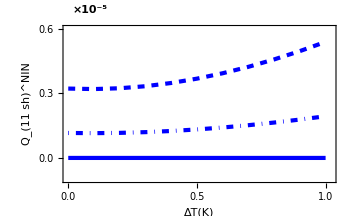

```mathematica
dataQn0Ts=Import["check300.dat"][[All,{1,6}]];
dataQn1Ts=Import["check301.dat"][[All,{1,6}]];
dataQn3Ts=Import["check302.dat"][[All,{1,6}]];
Needs["PlotLegends`"]
AQnTs=ListLinePlot[{dataQn0Ts,dataQn1Ts,dataQn3Ts},Frame->True,PlotRange->{{3,4.02},{-0.000001,0.000006}},Frame->True,FrameLabel->{Style["ΔT(K)",13,Bold,Black],Style["Q_(11  sh)^NIN",13,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,11],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.000006,"0.6"},{0.000003,"0.3"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{77,6},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-5",Black,11,Bold],Scaled[{0.1,1.1}]]}]
```

# Quantum noise in NIS setup for Z = (0, 1, 3) and T2 = 3 with respect to ΔT

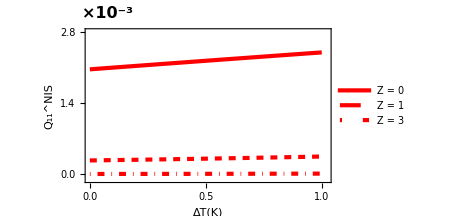

```mathematica
dataQs0T=Import["check300.dat"][[All,{1,4}]];
dataQs1T=Import["check301.dat"][[All,{1,4}]];
dataQs3T=Import["check302.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
AQsT=ListLinePlot[{dataQs0T,dataQs1T,dataQs3T},Frame->True,PlotRange->{{3,4.02},{-0.0001,0.0028}},Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Center,Center}],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["Q_11^NIS",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.0014,"1.4"},{0.0028,"2.8"}},None},{{{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{77,6},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,16,Bold],Scaled[{0.09,1.1}]]}]
```

```mathematica
xyMinMax={{0.2,1.001},{-.2,0.5}};


ListLinePlot[{dataQs0T,dataQs1T,dataQs3T},Frame->True,PlotRange->{{3,4.02},{-0.0001,0.0028}},Frame->True,FrameLabel->{Style["ΔT(K)",20,Bold,Black],Style["Q_11^NIS",20,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.0014,"1.4"},{0.0028,"2.8"}},None},{{{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->360,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[AQnT1,Scaled[{0.52,0.34}],Scaled[{0,0}],.7],PlotRange->{0.2,0.3},PlotRangeClipping->False},ImagePadding->{{77,7},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,11,Bold],Scaled[{0.09,1.1}]]}]
```

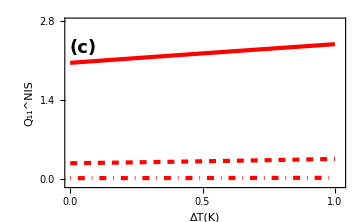

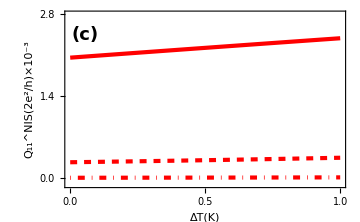

# Quantum thermal noise in NIS setup for Z = (0, 1, 3) and T2 = 3 with respect to ΔT

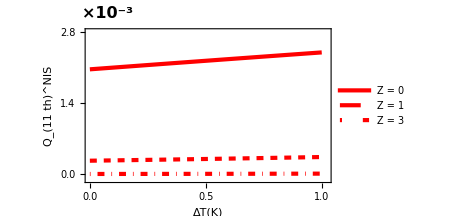

```mathematica
dataQs0Th=Import["check300.dat"][[All,{1,2}]];
dataQs1Th=Import["check301.dat"][[All,{1,2}]];
dataQs3Th=Import["check302.dat"][[All,{1,2}]];
Needs["PlotLegends`"]
AQsTh=ListLinePlot[{dataQs0Th,dataQs1Th,dataQs3Th},Frame->True,PlotRange->{{3,4.02},{-0.0001,0.0028}},Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Center,Center}],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["Q_(11  th)^NIS",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.0014,"1.4"},{0.0028,"2.8"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{77,8},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,16,Bold],Scaled[{0.09,1.1}]]}]
```

```mathematica
xyMinMax={{0.2,1.001},{-.2,0.5}};


ListLinePlot[{dataQs0Th,dataQs1Th,dataQs3Th},Frame->True,PlotRange->{{3,4.02},{-0.0001,0.0028}},Frame->True,FrameLabel->{Style["ΔT(K)",20,Bold,Black],Style["Q_(11  th)^NIS",20,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.0014,"1.4"},{0.0028,"2.8"}},None},{{{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->360,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[AQnTh,Scaled[{0.52,0.34}],Scaled[{0,0}],.7],PlotRange->{0.2,0.3},PlotRangeClipping->False},ImagePadding->{{77,7},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,11,Bold],Scaled[{0.09,1.1}]]}]
```

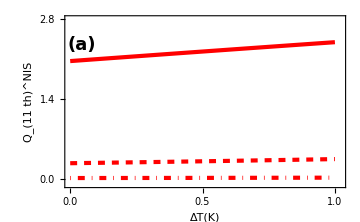

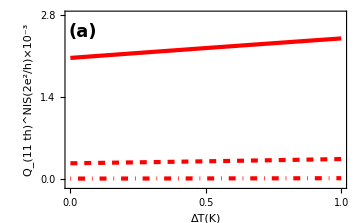

# Quantum shot noise in NIS setup for Z = (0, 1, 3) and T2 = 3 with respect to ΔT

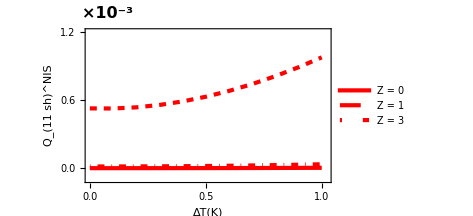

```mathematica
dataQs0Ts=Import["check300.dat"][[All,{1,3}]];
dataQs1Ts=Import["check301.dat"][[All,{1,3}]];
dataQs3Ts=Import["check302.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
AQsTs=ListLinePlot[{dataQs0Ts,dataQs1Ts,dataQs3Ts},Frame->True,PlotRange->{{3,4.02},{-0.000001,0.000012}},Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Center,Top}],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["Q_(11  sh)^NIS",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.000012,"1.2"},{0.000006,"0.6"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{77,7},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,16,Bold],Scaled[{0.09,1.1}]]}]
```

```mathematica
xyMinMax={{0.2,1.001},{-.2,0.5}};


ListLinePlot[{dataQs0Ts,dataQs1Ts,dataQs3Ts},Frame->True,PlotRange->{{3,4.02},{-0.000001,0.00001}},Frame->True,FrameLabel->{Style["ΔT(K)",20,Bold,Black],Style["Q_(11  sh)^NIS",20,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.00001,"1.0"},{0.000005,"0.5"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->370,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[AQnTs,Scaled[{0.5,0.3}],Scaled[{0,0}],.73],PlotRange->{0.2,0.3},PlotRangeClipping->False},ImagePadding->{{77,7},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-5",Black,16,Bold],Scaled[{0.09,1.1}]]}]
```

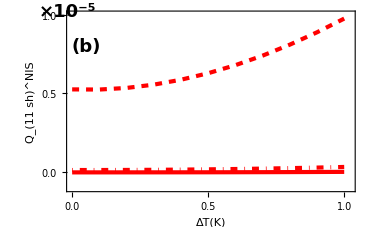

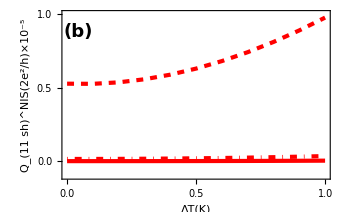

# Ratio of quantum noise in NIS and NIN for different Z as a function of ΔT

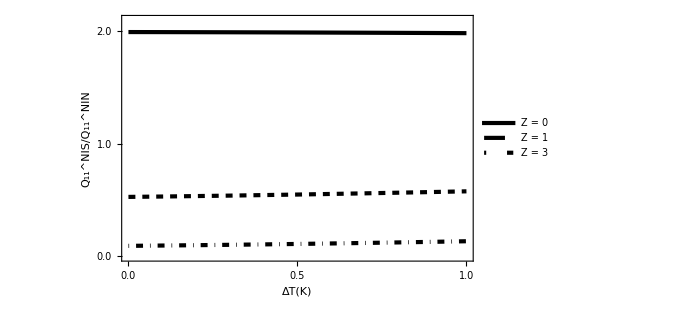

```mathematica
data1=Import["check300.dat"][[All,{1,8}]];
data2=Import["check301.dat"][[All,{1,8}]];
data3=Import["check302.dat"][[All,{1,8}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->{{3,4},{0.000,2.1}},Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Center,Center}],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["Q_11^NIS/Q_11^NIN",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Black,Dashed],Directive[AbsoluteThickness[3],Opacity[1],Black,DotDashed]},FrameTicks->{{{{0.000,"0.0"},{1.0,"1.0"},{2,"2.0"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->350,LabelStyle->Directive[Bold,Black,15]]
```